#### BC_DirectPath.nb (formerly TrivPathToIso.nb) Find the shortest (direct) path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ChooseTmat.nb, then this notebook Variables to change: Tmat, dt, ListSigma

#### choose Tmat

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrownAn00;
```

#### check that it’s symmetric, display info

```mathematica
MatrixNote[Tmat]
Tmat==Transpose[Tmat]
PrintVoigt[Tmat]
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

## Specify start/end elastic maps and Sigmas

#### Set of Sigmas to use For the plotting, it’d be helpful to list these in order from TRIV (smallest beta) to ISO (largest beta). These ListSigma will get over-written by the Special Cases below.

```mathematica
ListSigma={ORTH,TET};
```

```mathematica
ListSigma={ISO,CUBE,XISO,TRIG,TET,ORTH,MONO,TRIV};
```

```mathematica
ListSigma={MONO,ISO};
```

```mathematica
ListSigma={MONO,XISO,ISO};
```

```mathematica
ListSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};  (* default *)
```

#### Closest T to ISO

```mathematica
MatrixNote[Tmat]
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =Closest[Tmat,ISO];  (* ProjToVSigOfU[Tmat,id,ISO]*)
MatrixForm[TISO]
```

#### defaults for custom plotting (these will get overwritten below)

```mathematica
Sig1=TRIV;
Sig2=ISO;
ttop = 0.5;
```

#### choose t values (note: you can choose to use t1 < 0 for most of the maps in ChooseTmat.nb)

```mathematica
Print["minimum allowable t is t1 = ",tpertTmat[Tmat] ];
```

```mathematica
(* Ranget=Join[{0},Range[t1,t2,dt],{1}] *)
```

```mathematica
t1 = 0.; t2 = 1.;
dt=0.2; 
(*dt=0.05;*)
(* t1 = 0.8; t2 = 0.9;dt=0.01; *)
Ranget=Range[t1,t2,dt];
```

#### BrownAn00

```mathematica
(* t1 = -0.6;t2 = 1;dt=0.2; 
Ranget=Range[t1,t2,dt]; *)
```

#### Special Case 1: BrownAn00 TET triangle (supp1) TET to XISO segment for the Brown map Here TXISO is the closest to TRIV (nm2), and β_XISO = 20.35^o

```mathematica
(* MatrixNote[Tmat]
Sig1=TET;
Sig2=XISO;
MinmizationFacts[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
MinmizationFacts[Tmat,Sig2]
TXISO=Closest[Tmat,Sig2];
Tmat1=TTET;
Tmat2=TXISO; 
ListSigma={TET}; (* TET will give the triangle *)
ListSigma={MONO,TET,XISO}; 
ttop = 0.611707; *)
```

#### Special Case 2: BrownAn00 TET parabola (supp2) TET to CUBE segment for the Brown map Here TCUBE is the closest to TRIV (nm2), and β_CUBE = 24.34^o

```mathematica
(*MatrixNote[Tmat]
Sig1=TET;
Sig2=CUBE; 
MinmizationFacts[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
MinmizationFacts[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTET ;
Tmat2=TCUBE;
ListSigma={MONO,TET};*)
```

#### Special Case 3: BrownAn00 TRIG triangle (supp3) TRIG to CUBE segment for the Brown map Here CUBE is the closest to TRIV (nm2), and β_CUBE = 21.12^o

```mathematica
(*MatrixNote[Tmat]
Sig1=TRIG;
Sig2=CUBE; 
MinmizationFacts[Tmat,Sig1]
TTRIG=Closest[Tmat,Sig1];
MinmizationFacts[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTRIG;
Tmat2=TCUBE;
ListSigma={MONO,TET,TRIG};
ttop=0.53515;*)
```

#### Special Case 4: BrownAn00 TET triangle (supp4) Experiment with different U to see if the triangle is sustained.

```mathematica
(*MatrixNote[Tmat]
MinmizationFacts[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
(* UforNM1=UXISO.ZRot[25Degree]; *)
(* UforNM1=UXISO.XRot[1Degree].YRot[1Degree].ZRot[1Degree]; *)
Sig1=ORTH;
Sig2=TET;
TORTH=ProjToVSigOfU[Tmat,UforNM1,Sig1];
TTET=ProjToVSigOfU[Tmat,UforNM1,Sig2];
Tmat1=TORTH;
Tmat2=TTET; 
ListSigma={TET};  (* no need to run MONO here, since betaMONO = 0 by design *)
ttop=0.310400;*)
```

#### Special Case 5: Igel XISO inverted triangle (supp5) version 1: t1=0, t2=1, dt=0.05 version 2: t1=0.8, t2=0.9, dt=0.01

```mathematica
(*MatrixNote[Tmat]
MinmizationFacts[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
Sig1=TET;
Sig2=CUBE;
TTET=ProjToVSigOfU[Tmat,UforNM1,Sig1];
TCUBE=ProjToVSigOfU[Tmat,UforNM1,Sig2];
Tmat1=TTET;
Tmat2=TCUBE; 
ListSigma={XISO};   (* no need to run MONO here, since betaMONO = 0 by design *)
ttop=0.8499757596500602;  (* solved in BC_XISObetweenTETandCUBE.nb *)*)
```

#### Special Case 6: SSA2023 TET and ORTH curves

```mathematica
(*MatrixNote[Tmat]
Sig1=MONO;
Sig2=TRIG;
MinmizationFacts[Tmat,Sig1]
TMONO=Closest[Tmat,Sig1];
MinmizationFacts[Tmat,Sig2]
TTRIG=Closest[Tmat,Sig2];
Tmat1=TMONO;
Tmat2=TTRIG; 
ListSigma={MONO,ORTH,TET};*)
```

#### Choose Tmat1 (low symmetry) and Tmat2 (high symmetry)

```mathematica
MatrixNote[Tmat]
Tmat1 =Closest[Tmat,Sig1];
Tmat2 =Closest[Tmat,Sig2];
```

#### check endpoints (but note that your chosen t values may exclude the endpoints)

```mathematica
MatrixNote[Tmat]
DispMat[Tmat1,2]
DispMat[TT[0,Tmat1,Tmat2],2]
DispMat[Tmat2,2]
DispMat[TT[1,Tmat1,Tmat2],2]
```

#### min and max values of t (these are used for plotting)

```mathematica
Ranget
tmin=Ranget[[1]]
tmax=Ranget[[Length[Ranget]]]
```

#### Display the set of Tmats as BB and as Voigt

```mathematica
MatrixNote[Tmat]
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

## Check between distances, angles, and norms

```mathematica
MatrixNote[Tmat]
Ranget
```

#### changing the size of the elastic map changes distances but not angles

```mathematica
(*Tmat=2TmatBrownAn00;*)
```

#### choose a Sigma (choosing ISO will be instant; anything else may take time)

```mathematica
Sigx=ISO; (* something non-ISO is a better check, but it will require minimizations *)
```

#### check on distances (linear with t)

```mathematica
dT[TT[#,Tmat1,Tmat2],Sigx]&/@Ranget
Abs[1-#]NormMatrix[Tmat-Closest[Tmat,Sigx]]&/@Ranget
```

#### beta angles

```mathematica
βT[TT[#,Tmat1,Tmat2],Sigx]/Degree&/@Ranget
```

#### norm of the elastic maps (independent of Sigx) -- these vary

```mathematica
NormMatrix[TT[#,Tmat1,Tmat2]]&/@Ranget
```

#### check: calculate the distances from the angles and norms

```mathematica
Sin[βT[TT[#,Tmat1,Tmat2],Sigx]]NormMatrix[TT[#,Tmat,TISO]]&/@Ranget
```

#### check if the U’s are in D8 (as expected for TET)

```mathematica
(*ipick=3;
Ranget[[ipick]]
Tx=TT[Ranget[[ipick]],Tmat,TISO];
U1 =UT[Tmat,TET];
U2=UT[Tx,TET];
MatrixForm[Tmat]
MatrixForm[Tx]
MatrixForm[U1]
MatrixForm[U2]
MatrixForm[Transpose[U1].U2]
MatrixForm/@D8*)
```

## Optional: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* MinimizationFacts[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
MinimizationFacts[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with Tmat in its original orientation

```mathematica
Ux=IdentityMatrix[3];
Ubarx=MatrixUbar[Ux];
```

## Optional: Plot the balls

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
```

```mathematica
contours[Tmat,MONO]
MaxForScaling[Tmat,MONO]
```

#### plot the 4th ball

```mathematica
If[False,Show[cpMONO[TT[Ranget[[4]],Tmat1,Tmat2],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]]
```

#### plot all the balls (see also BC_PlotElasticMaps.nb) The isotropic ball, if plotted, will not look good; instead, a solid-colored sphere can be plotted.

```mathematica
If[False,Column[Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]&/@Ranget]]
```

## Calculate distance to each symmetry class Note: MinimizationFacts will re-run any minimizations, so we want to call βT instead.

```mathematica
Ranget
```

```mathematica
ListSigma
```

```mathematica
(* MinimizationFacts[TT[Ranget[[1]],Tmat1,Tmat2],ListSigma[[1]]] *) (* example of one MinimizationFacts *)
```

```mathematica
(*Do[(Print["t = ",Ranget[[i]]];MinimizationFacts[TT[Ranget[[i]],Tmat1,Tmat2],#])&/@ListSigma,{i,1,Length[Ranget]}]*)
```

```mathematica
Do[Print["t = ",Ranget[[i]]];
Do[Print["Σ = ",Σ,", βT = ",βT[TT[Ranget[[i]],Tmat1,Tmat2],Σ]/Degree],{Σ,ListSigma}],{i,1,Length[Ranget]}]
```

## Beta curves

```mathematica
ipick =Length[ListSigma];
ListSigma
Sigpick=ListSigma[[ipick]]
MatrixNote[Tmat]
Ranget
```

```mathematica
ColumnForm[{PaddedForm[#,{2,2}],Round[βT[TT[#,Tmat1,Tmat2],Sigpick]/Degree,.001]}&/@Ranget]
```

#### Angle in radians between Tmat and the closest-Sigma to Tmat is βT[Tmat, Sigma]

```mathematica
MatrixNote[Tmat]
βT[Tmat,Sigpick]
%/Degree
```

#### KEY: Choose which quantity to plot

```mathematica
pfun1[t_,Σ_]:=βT[TT[t,Tmat1,Tmat2],Σ]/Degree
pfun2[t_,Σ_]:=Sin[βT[TT[t,Tmat1,Tmat2],Σ]]
pfun3[t_,Σ_]:=dT[TT[t,Tmat1,Tmat2],Σ]
```

```mathematica
pfun[t_,Σ_]:=pfun3[t,Σ]; ylab="d_Σ(t), GPa";
```

```mathematica
pfun[t_,Σ_]:=pfun2[t,Σ]; ylab="Sin[ β_Σ(t) ]";
```

```mathematica
pfun[t_,Σ_]:=pfun1[t,Σ]; ylab="β_Σ(t), degrees";
```

#### Plot all the beta curves together. This simple plot should always work

```mathematica
(* BcurvePts[Sigma_]:={#,βT[TT[#,Tmat1,Tmat2],Sigma]/Degree}&/@Ranget *)
```

```mathematica
BcurvePts[Sigma_,pfun_]:={#,pfun[#,Sigma]}&/@Ranget
```

```mathematica
(* Ranget *)
```

```mathematica
MatrixNote[Tmat]
ListSigma
Graphics[Line[BcurvePts[#,pfun]]&/@ListSigma,Axes->True,AspectRatio->1,ImageSize->200]
```

#### Or pick only one from ListSigma (see ipick above)

```mathematica
Graphics[Line[BcurvePts[Sigpick,pfun]],Axes->True,AspectRatio->1,ImageSize->200]
```

```mathematica
xran =Ranget[[Length[Ranget]]]-Ranget[[1]]
```

```mathematica
Max[Ranget]
```

```mathematica
Ranget
```

## Beta curves - fancy version

#### Get the two endpoints of a line parallel to the segment of the beta curve that ends at x=1. The beta curve is input as a set of (x,y) points in the array pts. This version requires there be a value of t=1 within Ranget (pts).

```mathematica
gettwopts[pts_]:=Module[{segment,tslope,yIntercept,tStart,tEnd,yStart,yEnd,lpts},segment=Select[Partition[pts,2,1],#[[2,1]]==1&][[1]];
tslope=(segment[[2,2]]-segment[[1,2]])/(segment[[2,1]]-segment[[1,1]]);
yIntercept=segment[[1,2]]-tslope segment[[1,1]];
tStart=First[pts][[1]];
tEnd=Last[pts][[1]];
yStart=tslope tStart+yIntercept;
yEnd=tslope tEnd+yIntercept;
lpts={{tStart,yStart},{tEnd,yEnd}};
lpts]
```

#### ORIGINAL: Get the two endpoints of a line parallel to the final segment of the beta curve, which is input as a set of (x,y) points [pts].

```mathematica
(*gettwopts[pts_]:=Module[{lastSegment,tslope,yIntercept,tStart,tEnd,yStart,yEnd,lpts},
lastSegment=Take[pts,-2];
tslope=(lastSegment[[2,2]]-lastSegment[[1,2]])/(lastSegment[[2,1]]-lastSegment[[1,1]]);
yIntercept=lastSegment[[1,2]]-tslope lastSegment[[1,1]];
tStart=First[pts][[1]];
tEnd=Last[pts][[1]];
yStart=tslope tStart+yIntercept;
yEnd=tslope tEnd+yIntercept;
lpts={{tStart,yStart},{tEnd,yEnd}};
lpts]*)
```

#### The fancier version has colored dots (hues are set in ChooseTmat.nb)

```mathematica
(*PtOnβcurve[t_,Σ_]:={t,βT[TT[t,Tmat1,Tmat2],Σ]/Degree};
BetaCurve[Ranget_,Σ_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ],{n,1,Length[Ranget]}]};*)
```

```mathematica
PtOnβcurve[t_,Σ_,pfun_]:={t,pfun[t,Σ]};
BetaCurve[Ranget_,Σ_,pfun_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ,pfun],{n,1,Length[Ranget]}]};
```

```mathematica
(*yvals=βT[TT[#,Tmat1,Tmat2],Last[ListSigma]]/Degree &/@ Ranget; (* based on the LAST Σ in the list *)*)
```

```mathematica
yvals=BcurvePts[Last[ListSigma],pfun][[All,2]] (* based on the LAST Σ in the list *)
```

```mathematica
ymin=Min[yvals];
ymin=0;
ymax=Max[yvals];
xmin=Min[Ranget];
xmax=Max[Ranget];
xran =xmax-xmin;
btextx=xmin-0.08xran; (* btextx=1.03tmax; *)
ylabelx=xmin-0.4xran; 
ylabely =0.5(ymin+ymax);
xlabelx=(Max[Ranget]+Min[Ranget])/2;
xlabely =-0.15ymax;
Klabely =xlabely/2;
```

#### Drop TRIV from the list (and from the plot)

```mathematica
PSigma=ListSigma
PSigma=Drop[ListSigma,1]
```

```mathematica
PlotDashedLines=True;
```

```mathematica
st1=If[Sig1===TRIV,"T",Subscript["K",SymbolName[Sig1]]];
st2=Subscript["K",SymbolName[Sig2]];
stit=Row[{MatrixNote[Tmat]," from ",st1," to ",st2,", t = ",First[Ranget]," to ",Last[Ranget]}]
```

```mathematica
Graphics[{PointSize[.02],Line[BcurvePts[#,pfun]]&/@PSigma,{HueOfΣ[#],BetaCurve[Ranget,#,pfun]}&/@PSigma,If[PlotDashedLines,{HueOfΣ[#],Dashed,Line[gettwopts[BcurvePts[#,pfun]]]}&/@PSigma],Text[Style[SequenceForm[#," (",Round[pfun[tmin,#],0.01],")"],{HueOfΣ[#],15}],(*the text*)
{btextx,pfun[tmin,#]},{1,0}]&/@PSigma,(*the location of the text*)
Text[Style[ylab,22],{ylabelx,ylabely},{0,0},{0,1}],(*y-axis label*)
Text[Style["t",22],{xlabelx,xlabely},{0,0}],(*x-axis label*)
Text[Framed[Style[st1,16],Background->White,FrameStyle->None,FrameMargins->Medium],{0,Klabely}],Text[Framed[Style[st2,16],Background->White,FrameStyle->None,FrameMargins->Medium],{1,Klabely}],
If[First[Ranget]<0,Line[{{0,0},{0,ymax}}]],(*Vertical line at t=0*)
If[Last[Ranget]>1,Line[{{1,0},{1,ymax}}]]  (*Vertical line at t=1*)
},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->600,GridLines->False,
PlotLabel->Style[stit,22,Black],TicksStyle->Directive[FontSize->16,Black],AxesStyle->Black]
```

## For reference

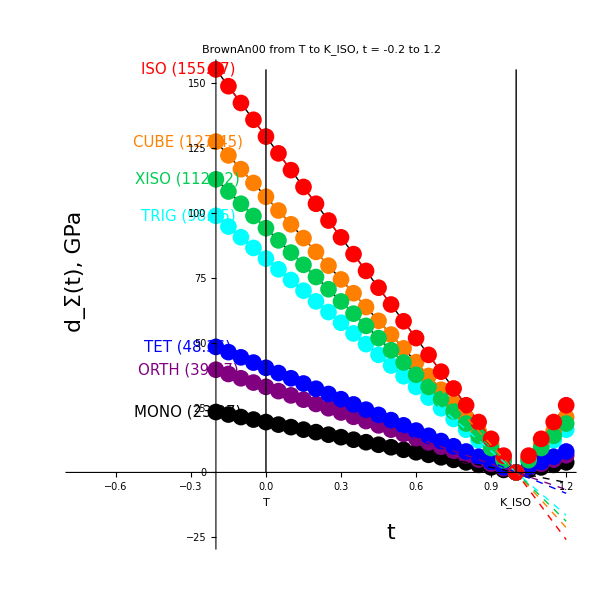

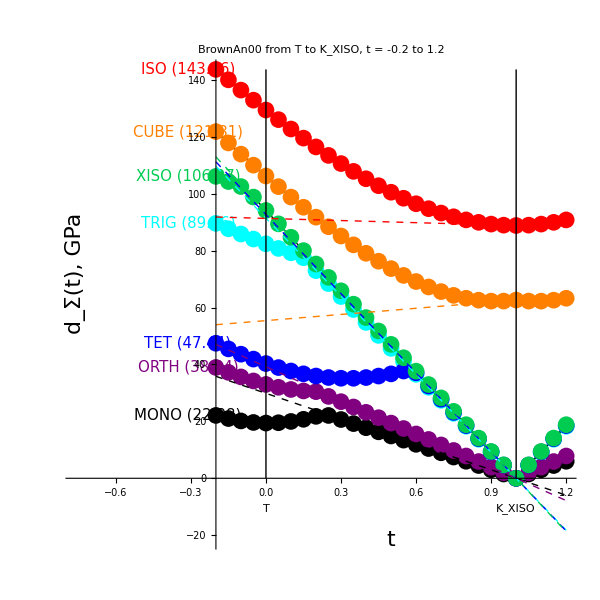

#### dt = 0.2, ListSigma = all

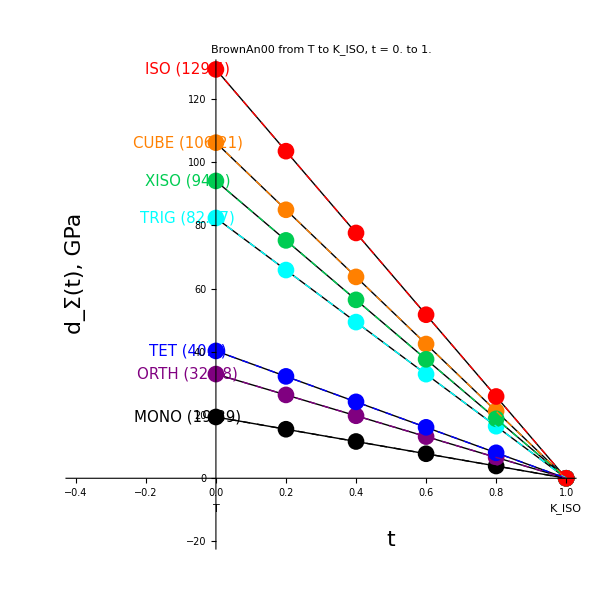

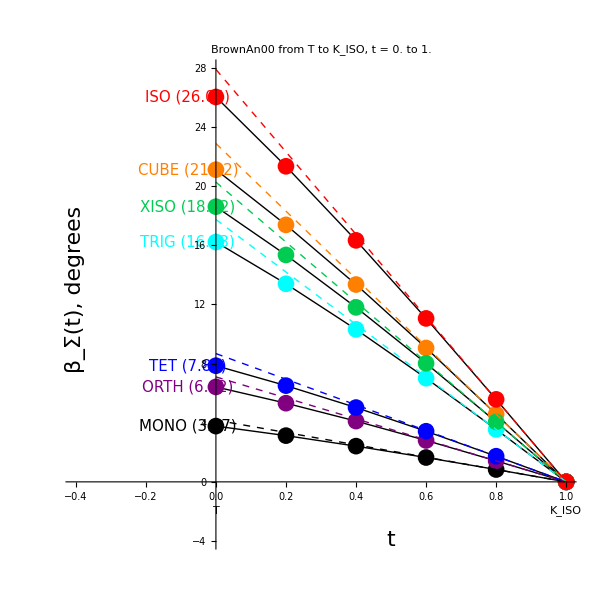

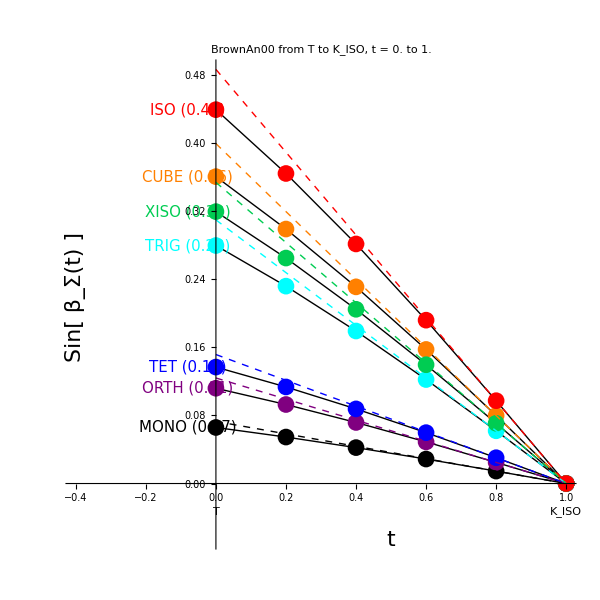

#### dt = 0.2, ListSigma = all

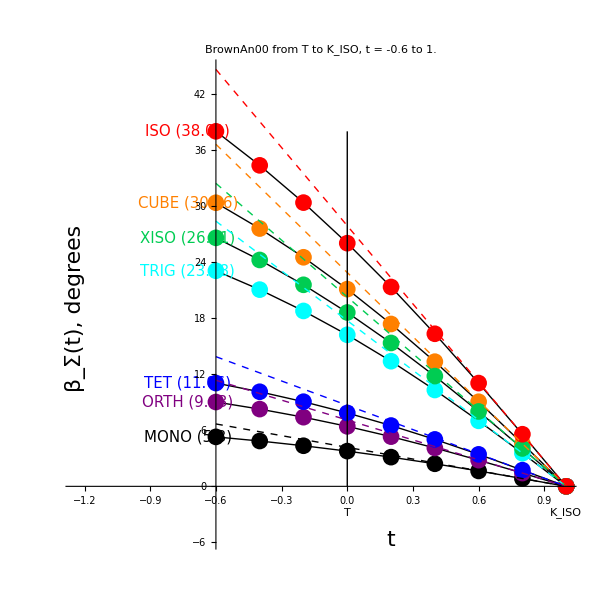

#### Brown: dt = 0.05, Tmat1=TTET, Tmat2=TXISO, ListSigma = {MONO,TET,XISO} [supp1]

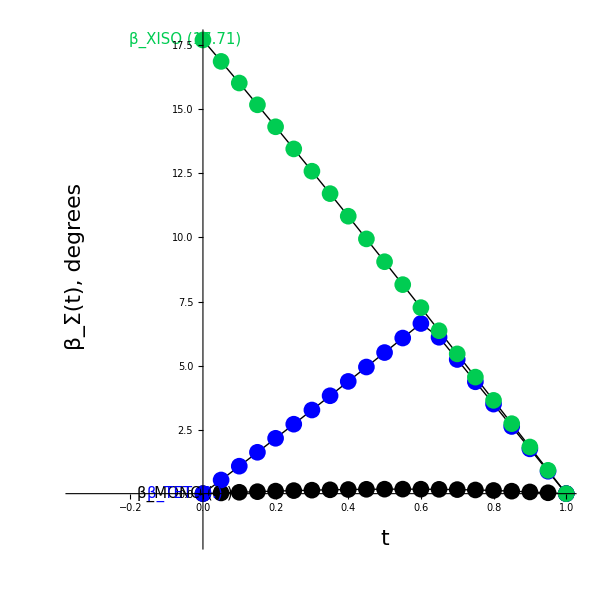

#### The maps from t=0 to t=1 are slightly trivial, as evidence from the small betaMONO angles:

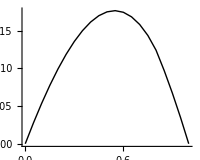

#### Brown: dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma={MONO,TET} [supp2]

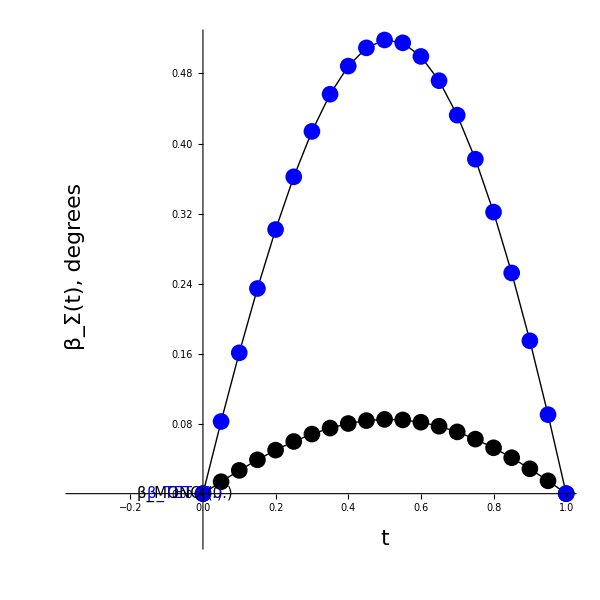

#### Brown: dt = 0.05, Tmat1=TTRIG, Tmat2=TCUBE, ListSigma={MONO,TET,TRIG} [supp3]

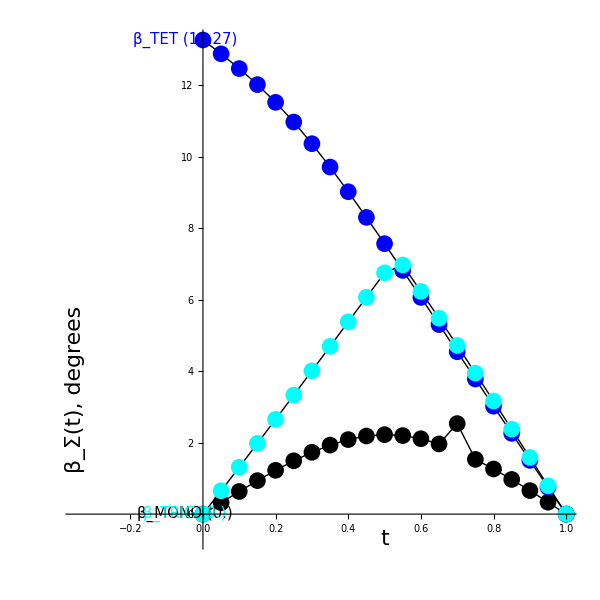

#### Brown dt = 0.05, Tmat1=TORTH, Tmat2=TTET, ListSigma = {TET}, nm1 with UforNM1 = UXISO [supp4]

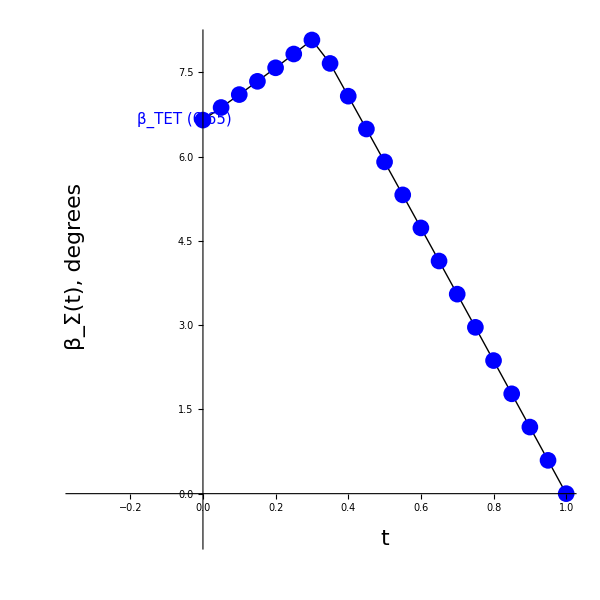

#### Igel dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma = {XISO}, nm1 with UforNM1 = UXISO [supp5]

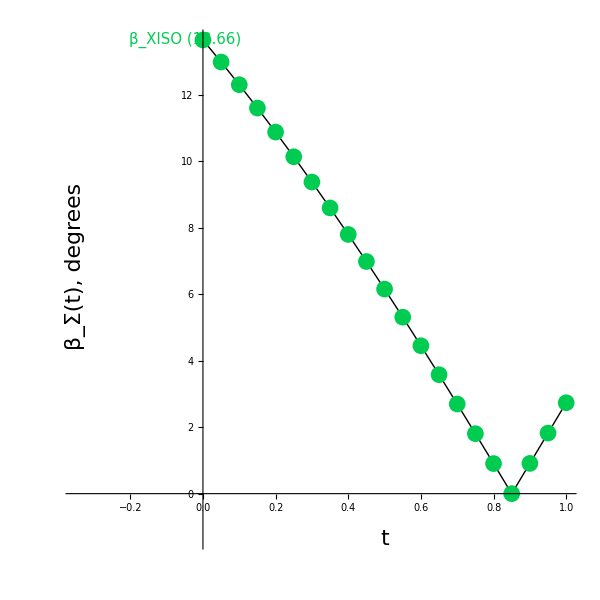

#### SSA2023 dt = 0.05, Tmat1=TMONO, Tmat2=TTRIG, ListSigma = {MONO,ORTH,TET}, nm2 [example 6]